# SemiEulerianGraphQ

Test if a connected undirected graph is semi-Eulerian

## Definition

```mathematica
ClearAll[SemiEulerianGraphQ]
SemiEulerianGraphQ[graph_?(ConnectedGraphQ[#]∧UndirectedGraphQ[#]&)]:=Count[VertexDegree[graph],x_/;OddQ[x]]<=2
```

## Documentation

### Usage

SemiEulerianGraphQ[graph]

Test if the connected undirected graph graph is semi-Eulerian

### Details & Options

The function tests if the number off vertices/nodes/points with odd degree is less than or equal to two.

If a graph is SemiEulerian, it is possible to traverse the graph crossing each edge exactly once without backtracking or retracing your steps if you can start and stop at different vertices.

The input graph needs to be an undirected graph. The input should also be a connected graph.

The function counts how many vertices have an odd degree. If this is less than or equal to 2, the graph is SemiEulerian. If the graph has more than 2 odd vertices, the graph is not semiEulerian. There always have to be an even number of vertices of odd degree.

An undirected graph is Eulerian is no vertices have odd degree and all vertices have even degreee. Euler proved this is a necessary condition and pointed out that this is also sufficient in his work on the bridges of Konigsburg at the academy in St. Petersburg in 1736. Hierholzer proved this condition is sufficient in a posthumous paper in 1873. This necessary and sufficient condition works for undirected graphs.

The function also works for multigraphs.

## Examples

### Basic Examples

Construct a graph with only two odd vertices and test if the graph is Semi-Eulerian:

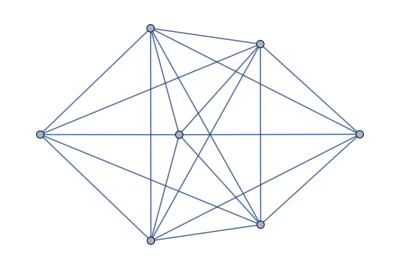

```mathematica
RandomGraph[{7,20}]
```

```mathematica
VertexDegree[RandomGraph[{7,20}]]
```

{6,6,6,5,6,5,6}

```mathematica
SemiEulerianGraphQ[RandomGraph[{7,20}]]
```

True

Test if the graph is also Eulerian:

```mathematica
EulerianGraphQ[RandomGraph[{7,20}]]
```

False

Test a graph with no odd vertices:

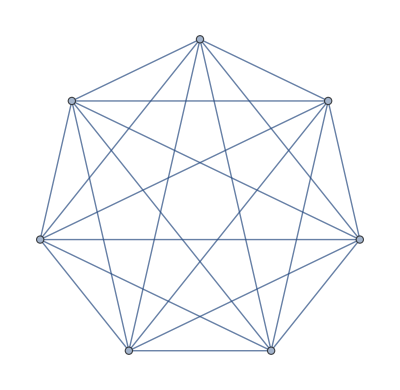

```mathematica
RandomGraph[{7,21}]
```

```mathematica
VertexDegree[RandomGraph[{7,21}]]
```

{6,6,6,6,6,6,6}

```mathematica
SemiEulerianGraphQ[RandomGraph[{7,21}]]
```

True

```mathematica
EulerianGraphQ[RandomGraph[{7,21}]]
```

True

Test a graph with more than two odd vertices:

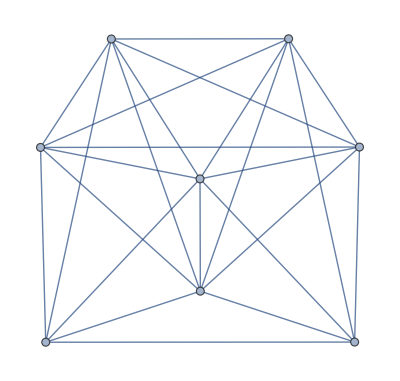

```mathematica
RandomGraph[{8,24}]
```

```mathematica
VertexDegree[RandomGraph[{8,24}]]
```

{7,6,6,5,5,7,6,6}

```mathematica
SemiEulerianGraphQ[RandomGraph[{8,24}]]
```

False

```mathematica
EulerianGraphQ[RandomGraph[{8,24}]]
```

False

### Scope

Text about additional examples expanding scope (and see other sections for options, applications, etc):

```mathematica
MyFunction[x,y,z]
```

x y z

### Options

### Applications

### Properties and Relations

Test if a buckyball graph is semi-Eulerian:

```mathematica
BuckyballGraph[]
```

-Graphics3D-

```mathematica
SemiEulerianGraphQ[BuckyballGraph[]]
```

False

Test if a torus graph is semi-Eulerian:

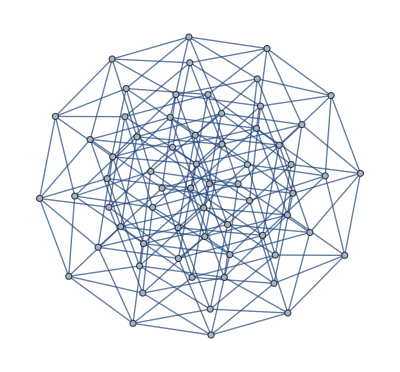

```mathematica
TorusGraph[{4,4,4}]
```

```mathematica
SemiEulerianGraphQ[TorusGraph[{4,4,4}]]
```

True

### Possible Issues

### Neat Examples

The bridges of Konigsburg multigraph is not semieulerian:

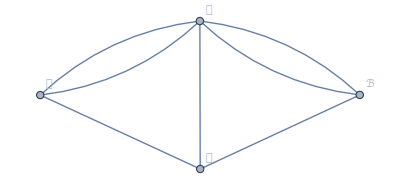

```mathematica
bridgesOfKonigsburg=Graph[{𝒜,ℬ,𝒞,𝒟},{𝒜<->ℬ,𝒜<->ℬ,𝒜<->𝒞,𝒜<->𝒞,𝒜<->𝒟,ℬ<->𝒟,𝒞<->𝒟},VertexLabels->Automatic]
```

```mathematica
SemiEulerianGraphQ[bridgesOfKonigsburg]
```

False

```mathematica
BuckyballGraph[]
```

-Graphics3D-

```mathematica
VertexDegree[BuckyballGraph[]]
```

{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3}

```mathematica
TorusGraph[{4,4,4}]
```

-Graphics-

```mathematica
VertexDegree[TorusGraph[{4,4,4}]]
```

{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6}

## Source & Additional Information

### Contributed By

Peter Cullen Burbery

### Keywords

Leonard Euler

Bridges of Konigsburg

Euler tours

Eulerizing graphs

Semi-Eulerian graphs

Eulerian graphs

Arc routing

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

EulerianGraphQ

VertexDegree

Count

### Related Resource Objects

MixedEulerianGraphQ

EulerizeGraph

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.1+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

I might add a way to test if a directed graph and mixed graph is semi Eulerian in the future.

## Submission Notes

Additional information for the reviewer.